# Chapter 1: Quantum measurement

## Author: Bruno O. Goes

#### 1) Useful functions

```mathematica
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";

MPLColorMap["Inferno"]
```

Function[x,Blend[{RGBColor[{0.00146159096, 0.000466127766, 0.01386552}],RGBColor[{0.00226726368, 0.00126992553, 0.018570352}],RGBColor[{0.00329899092, 0.00224934863, 0.0242390508}],RGBColor[{0.00454690615, 0.00339180156, 0.0309092475}],RGBColor[{0.00600552565, 0.00469194561, 0.038557898}],RGBColor[{0.00767578856, 0.00613611626, 0.0468360336}],RGBColor[{0.00956051094, 0.00771344131, 0.0551430756}],RGBColor[{0.0116634769, 0.00941675403, 0.063459808}],RGBColor[{0.0139950388, 0.0112247138, 0.071861689}],RGBColor[{0.0165605595, 0.0131362262, 0.0802817951}],RGBColor[{0.0193732295, 0.0151325789, 0.0887668094}],RGBColor[{0.0224468865, 0.0171991484, 0.0973274383}],RGBColor[{0.0257927373, 0.0193306298, 0.105929835}],RGBColor[{0.0294324251, 0.0215030771, 0.114621328}],RGBColor[{0.0333852235, 0.0237024271, 0.123397286}],RGBColor[{0.0376684211, 0.0259207864, 0.132232108}],RGBColor[{0.0422525554, 0.0281385015, 0.141140519}],RGBColor[{0.0469146287, 0.0303236129, 0.150163867}],RGBColor[{0.0516437624, 0.0324736172, 0.159254277}],RGBColor[{0.0564491009, 0.0345691867, 0.168413539}],RGBColor[{0.06133972, 0.0365900213, 0.177642172}],RGBColor[{0.066331262, 0.0385036268, 0.186961588}],RGBColor[{0.0714289181, 0.0402939095, 0.196353558}],RGBColor[{0.076636756, 0.0419053329, 0.205798788}],RGBColor[{0.0819620773, 0.0433278666, 0.215289113}],RGBColor[{0.0874113897, 0.0445561662, 0.224813479}],RGBColor[{0.0929901526, 0.0455829503, 0.234357604}],RGBColor[{0.0987024972, 0.0464018731, 0.2439037}],RGBColor[{0.104550936, 0.0470080541, 0.2534303}],RGBColor[{0.110536084, 0.0473986708, 0.262912235}],RGBColor[{0.116656423, 0.047573592, 0.272320803}],RGBColor[{0.122908126, 0.0475360183, 0.28162417}],RGBColor[{0.129284984, 0.0472930838, 0.290788012}],RGBColor[{0.13577845, 0.0468563678, 0.299776404}],RGBColor[{0.142377819, 0.0462422566, 0.30855291}],RGBColor[{0.149072957, 0.0454676444, 0.317085139}],RGBColor[{0.155849711, 0.0445588056, 0.325338414}],RGBColor[{0.162688939, 0.0435542881, 0.333276678}],RGBColor[{0.169575148, 0.0424893149, 0.340874188}],RGBColor[{0.176493202, 0.0414017089, 0.348110606}],RGBColor[{0.183428775, 0.0403288858, 0.354971391}],RGBColor[{0.190367453, 0.0393088888, 0.361446945}],RGBColor[{0.197297425, 0.0384001825, 0.367534629}],RGBColor[{0.204209298, 0.0376322609, 0.373237557}],RGBColor[{0.211095463, 0.0370296488, 0.378563264}],RGBColor[{0.217948648, 0.0366146049, 0.383522415}],RGBColor[{0.224762908, 0.0364049901, 0.388128944}],RGBColor[{0.231538148, 0.0364052511, 0.39240015}],RGBColor[{0.238272961, 0.0366209949, 0.396353388}],RGBColor[{0.244966911, 0.0370545017, 0.400006615}],RGBColor[{0.251620354, 0.0377052832, 0.403377897}],RGBColor[{0.258234265, 0.0385706153, 0.406485031}],RGBColor[{0.264809649, 0.0396468666, 0.409345373}],RGBColor[{0.271346664, 0.0409215821, 0.411976086}],RGBColor[{0.277849829, 0.0423528741, 0.414392106}],RGBColor[{0.284321318, 0.0439325787, 0.416607861}],RGBColor[{0.290763373, 0.0456437598, 0.418636756}],RGBColor[{0.297178251, 0.0474700293, 0.420491164}],RGBColor[{0.303568182, 0.0493958927, 0.422182449}],RGBColor[{0.309935342, 0.0514069729, 0.423720999}],RGBColor[{0.316281835, 0.0534901321, 0.425116277}],RGBColor[{0.322609671, 0.0556335178, 0.426376869}],RGBColor[{0.328920763, 0.0578265505, 0.427510546}],RGBColor[{0.335216916, 0.0600598734, 0.42852432}],RGBColor[{0.341499828, 0.0623252772, 0.429424503}],RGBColor[{0.347771086, 0.06461561, 0.430216765}],RGBColor[{0.354032169, 0.0669246832, 0.430906186}],RGBColor[{0.360284449, 0.0692471753, 0.431497309}],RGBColor[{0.366529195, 0.0715785403, 0.431994185}],RGBColor[{0.372767575, 0.0739149211, 0.432400419}],RGBColor[{0.379000659, 0.0762530701, 0.432719214}],RGBColor[{0.385228383, 0.0785914864, 0.432954973}],RGBColor[{0.391452659, 0.0809267058, 0.433108763}],RGBColor[{0.397674379, 0.0832568129, 0.433182647}],RGBColor[{0.403894278, 0.0855803445, 0.433178526}],RGBColor[{0.410113015, 0.0878961593, 0.433098056}],RGBColor[{0.416331169, 0.0902033992, 0.432942678}],RGBColor[{0.422549249, 0.0925014543, 0.432713635}],RGBColor[{0.428767696, 0.0947899342, 0.432411996}],RGBColor[{0.434986885, 0.0970686417, 0.432038673}],RGBColor[{0.441207124, 0.099337551, 0.431594438}],RGBColor[{0.447428382, 0.101597079, 0.431080497}],RGBColor[{0.453650614, 0.103847716, 0.430497898}],RGBColor[{0.459874623, 0.106089165, 0.429845789}],RGBColor[{0.466100494, 0.108321923, 0.429124507}],RGBColor[{0.472328255, 0.110546584, 0.42833432}],RGBColor[{0.478557889, 0.112763831, 0.427475431}],RGBColor[{0.484789325, 0.11497443, 0.426547991}],RGBColor[{0.491022448, 0.117179219, 0.425552106}],RGBColor[{0.497257069, 0.119379132, 0.424487908}],RGBColor[{0.503492698, 0.121575414, 0.42335611}],RGBColor[{0.509729541, 0.123768654, 0.422155676}],RGBColor[{0.515967304, 0.125959947, 0.420886594}],RGBColor[{0.522205646, 0.128150439, 0.419548848}],RGBColor[{0.528444192, 0.130341324, 0.418142411}],RGBColor[{0.534682523, 0.132533845, 0.416667258}],RGBColor[{0.540920186, 0.134729286, 0.415123366}],RGBColor[{0.547156706, 0.136928959, 0.413510662}],RGBColor[{0.553391649, 0.139134147, 0.411828882}],RGBColor[{0.559624442, 0.141346265, 0.410078028}],RGBColor[{0.565854477, 0.143566769, 0.408258132}],RGBColor[{0.572081108, 0.14579715, 0.406369246}],RGBColor[{0.578303656, 0.148038934, 0.404411444}],RGBColor[{0.584521407, 0.150293679, 0.402384829}],RGBColor[{0.590733615, 0.152562977, 0.400289528}],RGBColor[{0.596939751, 0.154848232, 0.398124897}],RGBColor[{0.60313893, 0.157151161, 0.395891308}],RGBColor[{0.609330184, 0.159473549, 0.393589349}],RGBColor[{0.615512627, 0.161817111, 0.391219295}],RGBColor[{0.62168534, 0.164183582, 0.388781456}],RGBColor[{0.627847374, 0.166574724, 0.38627618}],RGBColor[{0.633997746, 0.168992314, 0.383703854}],RGBColor[{0.640135447, 0.17143815, 0.381064906}],RGBColor[{0.646259648, 0.173913876, 0.378358969}],RGBColor[{0.652369348, 0.176421271, 0.375586209}],RGBColor[{0.658463166, 0.178962399, 0.372748214}],RGBColor[{0.664539964, 0.181539111, 0.369845599}],RGBColor[{0.670598572, 0.184153268, 0.366879025}],RGBColor[{0.676637795, 0.186806728, 0.363849195}],RGBColor[{0.682656407, 0.189501352, 0.360756856}],RGBColor[{0.688653158, 0.192238994, 0.357602797}],RGBColor[{0.694626769, 0.1950215, 0.354387853}],RGBColor[{0.700575937, 0.197850703, 0.3511129}],RGBColor[{0.706499709, 0.200728196, 0.347776863}],RGBColor[{0.712396345, 0.203656029, 0.344382594}],RGBColor[{0.718264447, 0.206635993, 0.340931208}],RGBColor[{0.724102613, 0.209669834, 0.337423766}],RGBColor[{0.729909422, 0.21275927, 0.333861367}],RGBColor[{0.735683432, 0.215905976, 0.330245147}],RGBColor[{0.741423185, 0.219111589, 0.326576275}],RGBColor[{0.747127207, 0.222377697, 0.322855952}],RGBColor[{0.752794009, 0.225705837, 0.31908541}],RGBColor[{0.75842209, 0.229097492, 0.31526591}],RGBColor[{0.76400994, 0.232554083, 0.311398734}],RGBColor[{0.769556038, 0.236076967, 0.307485188}],RGBColor[{0.775058888, 0.239667435, 0.303526312}],RGBColor[{0.780517023, 0.24332672, 0.299522665}],RGBColor[{0.785928794, 0.247055968, 0.295476756}],RGBColor[{0.791292674, 0.250856232, 0.291389943}],RGBColor[{0.796607144, 0.254728485, 0.287263585}],RGBColor[{0.801870689, 0.25867361, 0.283099033}],RGBColor[{0.807081807, 0.262692401, 0.278897629}],RGBColor[{0.812239008, 0.266785558, 0.274660698}],RGBColor[{0.817340818, 0.270953688, 0.270389545}],RGBColor[{0.822385784, 0.2751973, 0.266085445}],RGBColor[{0.827372474, 0.279516805, 0.261749643}],RGBColor[{0.832299481, 0.283912516, 0.257383341}],RGBColor[{0.837165425, 0.288384647, 0.2529877}],RGBColor[{0.841968959, 0.292933312, 0.248563825}],RGBColor[{0.846708768, 0.297558528, 0.244112767}],RGBColor[{0.851383572, 0.302260213, 0.239635512}],RGBColor[{0.85599213, 0.307038188, 0.235132978}],RGBColor[{0.860533241, 0.311892183, 0.230606009}],RGBColor[{0.865005747, 0.316821833, 0.226055368}],RGBColor[{0.869408534, 0.321826685, 0.221481734}],RGBColor[{0.87374053, 0.326906201, 0.216885699}],RGBColor[{0.878000715, 0.33205976, 0.212267762}],RGBColor[{0.882188112, 0.337286663, 0.207628326}],RGBColor[{0.886301795, 0.342586137, 0.202967696}],RGBColor[{0.890340885, 0.34795734, 0.19828608}],RGBColor[{0.894304553, 0.353399363, 0.193583583}],RGBColor[{0.898192017, 0.35891124, 0.188860212}],RGBColor[{0.902002544, 0.364491949, 0.184115876}],RGBColor[{0.905735448, 0.370140419, 0.179350388}],RGBColor[{0.90939009, 0.375855533, 0.174563472}],RGBColor[{0.912965874, 0.381636138, 0.169754764}],RGBColor[{0.916462251, 0.387481044, 0.164923826}],RGBColor[{0.91987871, 0.393389034, 0.160070152}],RGBColor[{0.923214783, 0.399358867, 0.155193185}],RGBColor[{0.926470039, 0.405389282, 0.150292329}],RGBColor[{0.929644083, 0.411479007, 0.145366973}],RGBColor[{0.932736555, 0.417626756, 0.140416519}],RGBColor[{0.935747126, 0.423831237, 0.135440416}],RGBColor[{0.938675494, 0.430091162, 0.130438175}],RGBColor[{0.941521384, 0.436405243, 0.12540944}],RGBColor[{0.944284543, 0.442772199, 0.120354038}],RGBColor[{0.946964741, 0.449190757, 0.115272059}],RGBColor[{0.949561766, 0.455659658, 0.110163947}],RGBColor[{0.952075421, 0.462177656, 0.105030614}],RGBColor[{0.954505523, 0.468743522, 0.0998735931}],RGBColor[{0.956851903, 0.475356048, 0.0946952268}],RGBColor[{0.959114397, 0.482014044, 0.0894989073}],RGBColor[{0.96129285, 0.488716345, 0.0842893891}],RGBColor[{0.96338711, 0.495461806, 0.0790731907}],RGBColor[{0.965397031, 0.502249309, 0.0738591143}],RGBColor[{0.967322465, 0.509077761, 0.0686589199}],RGBColor[{0.969163264, 0.515946092, 0.0634881971}],RGBColor[{0.970919277, 0.522853259, 0.058367489}],RGBColor[{0.972590351, 0.529798246, 0.0533237243}],RGBColor[{0.974176327, 0.536780059, 0.048392009}],RGBColor[{0.975677038, 0.543797733, 0.0436177922}],RGBColor[{0.977092313, 0.550850323, 0.0390500131}],RGBColor[{0.978421971, 0.557936911, 0.0349306227}],RGBColor[{0.979665824, 0.5650566, 0.0314091591}],RGBColor[{0.980823673, 0.572208516, 0.0285075931}],RGBColor[{0.981895311, 0.579391803, 0.0262497353}],RGBColor[{0.982880522, 0.586605627, 0.0246613416}],RGBColor[{0.983779081, 0.593849168, 0.0237702263}],RGBColor[{0.984590755, 0.601121626, 0.0236063833}],RGBColor[{0.985315301, 0.608422211, 0.0242021174}],RGBColor[{0.985952471, 0.615750147, 0.0255921853}],RGBColor[{0.986502013, 0.623104667, 0.0278139496}],RGBColor[{0.98696367, 0.630485011, 0.0309075459}],RGBColor[{0.987337182, 0.637890424, 0.0349160639}],RGBColor[{0.987622296, 0.645320152, 0.0398857472}],RGBColor[{0.987818759, 0.652773439, 0.0455808037}],RGBColor[{0.98792633, 0.660249526, 0.0517503867}],RGBColor[{0.987944783, 0.667747641, 0.0583286889}],RGBColor[{0.98787391, 0.675267, 0.0652570167}],RGBColor[{0.987713535, 0.682806802, 0.072489233}],RGBColor[{0.987463516, 0.690366218, 0.0799897176}],RGBColor[{0.987123759, 0.697944391, 0.0877314215}],RGBColor[{0.986694229, 0.705540424, 0.0956941797}],RGBColor[{0.98617497, 0.713153375, 0.103863324}],RGBColor[{0.985565739, 0.72078246, 0.112228756}],RGBColor[{0.984865203, 0.728427497, 0.120784651}],RGBColor[{0.984075129, 0.736086521, 0.129526579}],RGBColor[{0.983195992, 0.743758326, 0.138453063}],RGBColor[{0.982228463, 0.751441596, 0.147564573}],RGBColor[{0.981173457, 0.759134892, 0.156863224}],RGBColor[{0.980032178, 0.766836624, 0.166352544}],RGBColor[{0.978806183, 0.774545028, 0.176037298}],RGBColor[{0.977497453, 0.782258138, 0.185923357}],RGBColor[{0.976108474, 0.789973753, 0.196017589}],RGBColor[{0.974637842, 0.797691563, 0.206331925}],RGBColor[{0.973087939, 0.805409333, 0.216876839}],RGBColor[{0.971467822, 0.813121725, 0.227658046}],RGBColor[{0.969783146, 0.820825143, 0.238685942}],RGBColor[{0.968040817, 0.828515491, 0.249971582}],RGBColor[{0.966242589, 0.836190976, 0.261533898}],RGBColor[{0.964393924, 0.843848069, 0.273391112}],RGBColor[{0.962516656, 0.85147634, 0.285545675}],RGBColor[{0.960625545, 0.859068716, 0.298010219}],RGBColor[{0.958720088, 0.866624355, 0.310820466}],RGBColor[{0.956834075, 0.874128569, 0.323973947}],RGBColor[{0.954997177, 0.881568926, 0.337475479}],RGBColor[{0.953215092, 0.888942277, 0.351368713}],RGBColor[{0.951546225, 0.896225909, 0.365627005}],RGBColor[{0.950018481, 0.903409063, 0.380271225}],RGBColor[{0.948683391, 0.910472964, 0.395289169}],RGBColor[{0.947594362, 0.917399053, 0.410665194}],RGBColor[{0.946809163, 0.924168246, 0.426373236}],RGBColor[{0.946391536, 0.930760752, 0.442367495}],RGBColor[{0.946402951, 0.937158971, 0.458591507}],RGBColor[{0.946902568, 0.943347775, 0.474969778}],RGBColor[{0.947936825, 0.949317522, 0.491426053}],RGBColor[{0.94954483, 0.9550629, 0.507859649}],RGBColor[{0.951740304, 0.960586693, 0.524203026}],RGBColor[{0.954529281, 0.965895868, 0.540360752}],RGBColor[{0.957896053, 0.97100333, 0.55627509}],RGBColor[{0.96181202, 0.975924241, 0.571925382}],RGBColor[{0.966248822, 0.980678193, 0.587205773}],RGBColor[{0.971161622, 0.985282161, 0.60215433}],RGBColor[{0.976510983, 0.989753437, 0.616760413}],RGBColor[{0.982257307, 0.994108844, 0.631017009}],RGBColor[{0.988362068, 0.998364143, 0.644924005}]},x]]

```mathematica
(*Drawing the Poicaré sphere: based on Melt's code*)
PoincareSphere[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[N[angles],2 π];If[end≤start,end+=2 π];seg=Quotient[N[end-start],π/2];ϕ=Mod[N[end-start],π/2];If[seg==4,seg=3;ϕ=π/2];pts=(r RotationMatrix[start].#1&)/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],(RotationMatrix[(seg π)/2].#1&)/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];If[Length[m]==2,pts=(m+#1&)/@pts,pts=(m+#1&)/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];w=Join[Take[{1,1/(√2),1,1/(√2),1,1/(√2),1},2 seg+1],{Cos[ϕ/2],1}];k=Join[{0,0,0},(Riffle[#1,#1]&)[Range[seg+1]],{seg+1}];BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;pointsAndConnection[points_]:=(Sequence@@{Sequence@@Point/@#1,Line[#1]}&)[points];surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{0,1,0}],{0,0,0}}}];texKet[n_]:=Text[Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString[n]],FontFamily->"Times",20]];Graphics3D[{White,Opacity[0.3],Sphere[{0,0,0},1],Opacity[1],Thickness[0.004],PointSize[0.02],Red,pointsAndConnection[{{0,0,1},{0,0,-1}}],Blue,pointsAndConnection[{{1,0,0},{-1,0,0}}],Darker[Green],pointsAndConnection[{{0,1,0},{0,-1,0}}],Black,Point[{0,0,0}],If[labels==True,{Text[texKet["R"],{0,0,1.2}],Text[texKet["L"],{0,0,-1.2}],Text[texKet["H"],{1.2,0,0}],Text[texKet["V"],{-1.2,0,0}],Text[texKet["A"],{0,1.2,0}],Text[texKet["D"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]]
```

```mathematica
PoincareSphere[]
```

-Graphics3D-

```mathematica
(*Drawing the spin Bloch sphere: based on Melt's code*)
BlochSphereSpin[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[N[angles],2 π];If[end≤start,end+=2 π];seg=Quotient[N[end-start],π/2];ϕ=Mod[N[end-start],π/2];If[seg==4,seg=3;ϕ=π/2];pts=(r RotationMatrix[start].#1&)/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],(RotationMatrix[(seg π)/2].#1&)/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];If[Length[m]==2,pts=(m+#1&)/@pts,pts=(m+#1&)/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];w=Join[Take[{1,1/(√2),1,1/(√2),1,1/(√2),1},2 seg+1],{Cos[ϕ/2],1}];k=Join[{0,0,0},(Riffle[#1,#1]&)[Range[seg+1]],{seg+1}];BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;pointsAndConnection[points_]:=(Sequence@@{Sequence@@Point/@#1,Line[#1]}&)[points];surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{0,1,0}],{0,0,0}}}];texKet[n_]:=Text[Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString[n]],FontFamily->"Times",20]];Graphics3D[{White,Opacity[0.3],Sphere[{0,0,0},1],Opacity[1],Thickness[0.004],PointSize[0.02],Red,pointsAndConnection[{{0,0,1},{0,0,-1}}],Blue,pointsAndConnection[{{1,0,0},{-1,0,0}}],Darker[Green],pointsAndConnection[{{0,1,0},{0,-1,0}}],Black,Point[{0,0,0}],If[labels==True,{Text[texKet["↑"],{0,0,1.2}],Text[texKet["↓"],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["i"],{0,1.2,0}],Text[texKet["-i"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]]
```

```mathematica
BlochSphereSpin[]
```

-Graphics3D-

Function[x,Blend[{RGBColor[{0.00146159096, 0.000466127766, 0.01386552}],RGBColor[{0.00226726368, 0.00126992553, 0.018570352}],RGBColor[{0.00329899092, 0.00224934863, 0.0242390508}],RGBColor[{0.00454690615, 0.00339180156, 0.0309092475}],RGBColor[{0.00600552565, 0.00469194561, 0.038557898}],RGBColor[{0.00767578856, 0.00613611626, 0.0468360336}],RGBColor[{0.00956051094, 0.00771344131, 0.0551430756}],RGBColor[{0.0116634769, 0.00941675403, 0.063459808}],RGBColor[{0.0139950388, 0.0112247138, 0.071861689}],RGBColor[{0.0165605595, 0.0131362262, 0.0802817951}],RGBColor[{0.0193732295, 0.0151325789, 0.0887668094}],RGBColor[{0.0224468865, 0.0171991484, 0.0973274383}],RGBColor[{0.0257927373, 0.0193306298, 0.105929835}],RGBColor[{0.0294324251, 0.0215030771, 0.114621328}],RGBColor[{0.0333852235, 0.0237024271, 0.123397286}],RGBColor[{0.0376684211, 0.0259207864, 0.132232108}],RGBColor[{0.0422525554, 0.0281385015, 0.141140519}],RGBColor[{0.0469146287, 0.0303236129, 0.150163867}],RGBColor[{0.0516437624, 0.0324736172, 0.159254277}],RGBColor[{0.0564491009, 0.0345691867, 0.168413539}],RGBColor[{0.06133972, 0.0365900213, 0.177642172}],RGBColor[{0.066331262, 0.0385036268, 0.186961588}],RGBColor[{0.0714289181, 0.0402939095, 0.196353558}],RGBColor[{0.076636756, 0.0419053329, 0.205798788}],RGBColor[{0.0819620773, 0.0433278666, 0.215289113}],RGBColor[{0.0874113897, 0.0445561662, 0.224813479}],RGBColor[{0.0929901526, 0.0455829503, 0.234357604}],RGBColor[{0.0987024972, 0.0464018731, 0.2439037}],RGBColor[{0.104550936, 0.0470080541, 0.2534303}],RGBColor[{0.110536084, 0.0473986708, 0.262912235}],RGBColor[{0.116656423, 0.047573592, 0.272320803}],RGBColor[{0.122908126, 0.0475360183, 0.28162417}],RGBColor[{0.129284984, 0.0472930838, 0.290788012}],RGBColor[{0.13577845, 0.0468563678, 0.299776404}],RGBColor[{0.142377819, 0.0462422566, 0.30855291}],RGBColor[{0.149072957, 0.0454676444, 0.317085139}],RGBColor[{0.155849711, 0.0445588056, 0.325338414}],RGBColor[{0.162688939, 0.0435542881, 0.333276678}],RGBColor[{0.169575148, 0.0424893149, 0.340874188}],RGBColor[{0.176493202, 0.0414017089, 0.348110606}],RGBColor[{0.183428775, 0.0403288858, 0.354971391}],RGBColor[{0.190367453, 0.0393088888, 0.361446945}],RGBColor[{0.197297425, 0.0384001825, 0.367534629}],RGBColor[{0.204209298, 0.0376322609, 0.373237557}],RGBColor[{0.211095463, 0.0370296488, 0.378563264}],RGBColor[{0.217948648, 0.0366146049, 0.383522415}],RGBColor[{0.224762908, 0.0364049901, 0.388128944}],RGBColor[{0.231538148, 0.0364052511, 0.39240015}],RGBColor[{0.238272961, 0.0366209949, 0.396353388}],RGBColor[{0.244966911, 0.0370545017, 0.400006615}],RGBColor[{0.251620354, 0.0377052832, 0.403377897}],RGBColor[{0.258234265, 0.0385706153, 0.406485031}],RGBColor[{0.264809649, 0.0396468666, 0.409345373}],RGBColor[{0.271346664, 0.0409215821, 0.411976086}],RGBColor[{0.277849829, 0.0423528741, 0.414392106}],RGBColor[{0.284321318, 0.0439325787, 0.416607861}],RGBColor[{0.290763373, 0.0456437598, 0.418636756}],RGBColor[{0.297178251, 0.0474700293, 0.420491164}],RGBColor[{0.303568182, 0.0493958927, 0.422182449}],RGBColor[{0.309935342, 0.0514069729, 0.423720999}],RGBColor[{0.316281835, 0.0534901321, 0.425116277}],RGBColor[{0.322609671, 0.0556335178, 0.426376869}],RGBColor[{0.328920763, 0.0578265505, 0.427510546}],RGBColor[{0.335216916, 0.0600598734, 0.42852432}],RGBColor[{0.341499828, 0.0623252772, 0.429424503}],RGBColor[{0.347771086, 0.06461561, 0.430216765}],RGBColor[{0.354032169, 0.0669246832, 0.430906186}],RGBColor[{0.360284449, 0.0692471753, 0.431497309}],RGBColor[{0.366529195, 0.0715785403, 0.431994185}],RGBColor[{0.372767575, 0.0739149211, 0.432400419}],RGBColor[{0.379000659, 0.0762530701, 0.432719214}],RGBColor[{0.385228383, 0.0785914864, 0.432954973}],RGBColor[{0.391452659, 0.0809267058, 0.433108763}],RGBColor[{0.397674379, 0.0832568129, 0.433182647}],RGBColor[{0.403894278, 0.0855803445, 0.433178526}],RGBColor[{0.410113015, 0.0878961593, 0.433098056}],RGBColor[{0.416331169, 0.0902033992, 0.432942678}],RGBColor[{0.422549249, 0.0925014543, 0.432713635}],RGBColor[{0.428767696, 0.0947899342, 0.432411996}],RGBColor[{0.434986885, 0.0970686417, 0.432038673}],RGBColor[{0.441207124, 0.099337551, 0.431594438}],RGBColor[{0.447428382, 0.101597079, 0.431080497}],RGBColor[{0.453650614, 0.103847716, 0.430497898}],RGBColor[{0.459874623, 0.106089165, 0.429845789}],RGBColor[{0.466100494, 0.108321923, 0.429124507}],RGBColor[{0.472328255, 0.110546584, 0.42833432}],RGBColor[{0.478557889, 0.112763831, 0.427475431}],RGBColor[{0.484789325, 0.11497443, 0.426547991}],RGBColor[{0.491022448, 0.117179219, 0.425552106}],RGBColor[{0.497257069, 0.119379132, 0.424487908}],RGBColor[{0.503492698, 0.121575414, 0.42335611}],RGBColor[{0.509729541, 0.123768654, 0.422155676}],RGBColor[{0.515967304, 0.125959947, 0.420886594}],RGBColor[{0.522205646, 0.128150439, 0.419548848}],RGBColor[{0.528444192, 0.130341324, 0.418142411}],RGBColor[{0.534682523, 0.132533845, 0.416667258}],RGBColor[{0.540920186, 0.134729286, 0.415123366}],RGBColor[{0.547156706, 0.136928959, 0.413510662}],RGBColor[{0.553391649, 0.139134147, 0.411828882}],RGBColor[{0.559624442, 0.141346265, 0.410078028}],RGBColor[{0.565854477, 0.143566769, 0.408258132}],RGBColor[{0.572081108, 0.14579715, 0.406369246}],RGBColor[{0.578303656, 0.148038934, 0.404411444}],RGBColor[{0.584521407, 0.150293679, 0.402384829}],RGBColor[{0.590733615, 0.152562977, 0.400289528}],RGBColor[{0.596939751, 0.154848232, 0.398124897}],RGBColor[{0.60313893, 0.157151161, 0.395891308}],RGBColor[{0.609330184, 0.159473549, 0.393589349}],RGBColor[{0.615512627, 0.161817111, 0.391219295}],RGBColor[{0.62168534, 0.164183582, 0.388781456}],RGBColor[{0.627847374, 0.166574724, 0.38627618}],RGBColor[{0.633997746, 0.168992314, 0.383703854}],RGBColor[{0.640135447, 0.17143815, 0.381064906}],RGBColor[{0.646259648, 0.173913876, 0.378358969}],RGBColor[{0.652369348, 0.176421271, 0.375586209}],RGBColor[{0.658463166, 0.178962399, 0.372748214}],RGBColor[{0.664539964, 0.181539111, 0.369845599}],RGBColor[{0.670598572, 0.184153268, 0.366879025}],RGBColor[{0.676637795, 0.186806728, 0.363849195}],RGBColor[{0.682656407, 0.189501352, 0.360756856}],RGBColor[{0.688653158, 0.192238994, 0.357602797}],RGBColor[{0.694626769, 0.1950215, 0.354387853}],RGBColor[{0.700575937, 0.197850703, 0.3511129}],RGBColor[{0.706499709, 0.200728196, 0.347776863}],RGBColor[{0.712396345, 0.203656029, 0.344382594}],RGBColor[{0.718264447, 0.206635993, 0.340931208}],RGBColor[{0.724102613, 0.209669834, 0.337423766}],RGBColor[{0.729909422, 0.21275927, 0.333861367}],RGBColor[{0.735683432, 0.215905976, 0.330245147}],RGBColor[{0.741423185, 0.219111589, 0.326576275}],RGBColor[{0.747127207, 0.222377697, 0.322855952}],RGBColor[{0.752794009, 0.225705837, 0.31908541}],RGBColor[{0.75842209, 0.229097492, 0.31526591}],RGBColor[{0.76400994, 0.232554083, 0.311398734}],RGBColor[{0.769556038, 0.236076967, 0.307485188}],RGBColor[{0.775058888, 0.239667435, 0.303526312}],RGBColor[{0.780517023, 0.24332672, 0.299522665}],RGBColor[{0.785928794, 0.247055968, 0.295476756}],RGBColor[{0.791292674, 0.250856232, 0.291389943}],RGBColor[{0.796607144, 0.254728485, 0.287263585}],RGBColor[{0.801870689, 0.25867361, 0.283099033}],RGBColor[{0.807081807, 0.262692401, 0.278897629}],RGBColor[{0.812239008, 0.266785558, 0.274660698}],RGBColor[{0.817340818, 0.270953688, 0.270389545}],RGBColor[{0.822385784, 0.2751973, 0.266085445}],RGBColor[{0.827372474, 0.279516805, 0.261749643}],RGBColor[{0.832299481, 0.283912516, 0.257383341}],RGBColor[{0.837165425, 0.288384647, 0.2529877}],RGBColor[{0.841968959, 0.292933312, 0.248563825}],RGBColor[{0.846708768, 0.297558528, 0.244112767}],RGBColor[{0.851383572, 0.302260213, 0.239635512}],RGBColor[{0.85599213, 0.307038188, 0.235132978}],RGBColor[{0.860533241, 0.311892183, 0.230606009}],RGBColor[{0.865005747, 0.316821833, 0.226055368}],RGBColor[{0.869408534, 0.321826685, 0.221481734}],RGBColor[{0.87374053, 0.326906201, 0.216885699}],RGBColor[{0.878000715, 0.33205976, 0.212267762}],RGBColor[{0.882188112, 0.337286663, 0.207628326}],RGBColor[{0.886301795, 0.342586137, 0.202967696}],RGBColor[{0.890340885, 0.34795734, 0.19828608}],RGBColor[{0.894304553, 0.353399363, 0.193583583}],RGBColor[{0.898192017, 0.35891124, 0.188860212}],RGBColor[{0.902002544, 0.364491949, 0.184115876}],RGBColor[{0.905735448, 0.370140419, 0.179350388}],RGBColor[{0.90939009, 0.375855533, 0.174563472}],RGBColor[{0.912965874, 0.381636138, 0.169754764}],RGBColor[{0.916462251, 0.387481044, 0.164923826}],RGBColor[{0.91987871, 0.393389034, 0.160070152}],RGBColor[{0.923214783, 0.399358867, 0.155193185}],RGBColor[{0.926470039, 0.405389282, 0.150292329}],RGBColor[{0.929644083, 0.411479007, 0.145366973}],RGBColor[{0.932736555, 0.417626756, 0.140416519}],RGBColor[{0.935747126, 0.423831237, 0.135440416}],RGBColor[{0.938675494, 0.430091162, 0.130438175}],RGBColor[{0.941521384, 0.436405243, 0.12540944}],RGBColor[{0.944284543, 0.442772199, 0.120354038}],RGBColor[{0.946964741, 0.449190757, 0.115272059}],RGBColor[{0.949561766, 0.455659658, 0.110163947}],RGBColor[{0.952075421, 0.462177656, 0.105030614}],RGBColor[{0.954505523, 0.468743522, 0.0998735931}],RGBColor[{0.956851903, 0.475356048, 0.0946952268}],RGBColor[{0.959114397, 0.482014044, 0.0894989073}],RGBColor[{0.96129285, 0.488716345, 0.0842893891}],RGBColor[{0.96338711, 0.495461806, 0.0790731907}],RGBColor[{0.965397031, 0.502249309, 0.0738591143}],RGBColor[{0.967322465, 0.509077761, 0.0686589199}],RGBColor[{0.969163264, 0.515946092, 0.0634881971}],RGBColor[{0.970919277, 0.522853259, 0.058367489}],RGBColor[{0.972590351, 0.529798246, 0.0533237243}],RGBColor[{0.974176327, 0.536780059, 0.048392009}],RGBColor[{0.975677038, 0.543797733, 0.0436177922}],RGBColor[{0.977092313, 0.550850323, 0.0390500131}],RGBColor[{0.978421971, 0.557936911, 0.0349306227}],RGBColor[{0.979665824, 0.5650566, 0.0314091591}],RGBColor[{0.980823673, 0.572208516, 0.0285075931}],RGBColor[{0.981895311, 0.579391803, 0.0262497353}],RGBColor[{0.982880522, 0.586605627, 0.0246613416}],RGBColor[{0.983779081, 0.593849168, 0.0237702263}],RGBColor[{0.984590755, 0.601121626, 0.0236063833}],RGBColor[{0.985315301, 0.608422211, 0.0242021174}],RGBColor[{0.985952471, 0.615750147, 0.0255921853}],RGBColor[{0.986502013, 0.623104667, 0.0278139496}],RGBColor[{0.98696367, 0.630485011, 0.0309075459}],RGBColor[{0.987337182, 0.637890424, 0.0349160639}],RGBColor[{0.987622296, 0.645320152, 0.0398857472}],RGBColor[{0.987818759, 0.652773439, 0.0455808037}],RGBColor[{0.98792633, 0.660249526, 0.0517503867}],RGBColor[{0.987944783, 0.667747641, 0.0583286889}],RGBColor[{0.98787391, 0.675267, 0.0652570167}],RGBColor[{0.987713535, 0.682806802, 0.072489233}],RGBColor[{0.987463516, 0.690366218, 0.0799897176}],RGBColor[{0.987123759, 0.697944391, 0.0877314215}],RGBColor[{0.986694229, 0.705540424, 0.0956941797}],RGBColor[{0.98617497, 0.713153375, 0.103863324}],RGBColor[{0.985565739, 0.72078246, 0.112228756}],RGBColor[{0.984865203, 0.728427497, 0.120784651}],RGBColor[{0.984075129, 0.736086521, 0.129526579}],RGBColor[{0.983195992, 0.743758326, 0.138453063}],RGBColor[{0.982228463, 0.751441596, 0.147564573}],RGBColor[{0.981173457, 0.759134892, 0.156863224}],RGBColor[{0.980032178, 0.766836624, 0.166352544}],RGBColor[{0.978806183, 0.774545028, 0.176037298}],RGBColor[{0.977497453, 0.782258138, 0.185923357}],RGBColor[{0.976108474, 0.789973753, 0.196017589}],RGBColor[{0.974637842, 0.797691563, 0.206331925}],RGBColor[{0.973087939, 0.805409333, 0.216876839}],RGBColor[{0.971467822, 0.813121725, 0.227658046}],RGBColor[{0.969783146, 0.820825143, 0.238685942}],RGBColor[{0.968040817, 0.828515491, 0.249971582}],RGBColor[{0.966242589, 0.836190976, 0.261533898}],RGBColor[{0.964393924, 0.843848069, 0.273391112}],RGBColor[{0.962516656, 0.85147634, 0.285545675}],RGBColor[{0.960625545, 0.859068716, 0.298010219}],RGBColor[{0.958720088, 0.866624355, 0.310820466}],RGBColor[{0.956834075, 0.874128569, 0.323973947}],RGBColor[{0.954997177, 0.881568926, 0.337475479}],RGBColor[{0.953215092, 0.888942277, 0.351368713}],RGBColor[{0.951546225, 0.896225909, 0.365627005}],RGBColor[{0.950018481, 0.903409063, 0.380271225}],RGBColor[{0.948683391, 0.910472964, 0.395289169}],RGBColor[{0.947594362, 0.917399053, 0.410665194}],RGBColor[{0.946809163, 0.924168246, 0.426373236}],RGBColor[{0.946391536, 0.930760752, 0.442367495}],RGBColor[{0.946402951, 0.937158971, 0.458591507}],RGBColor[{0.946902568, 0.943347775, 0.474969778}],RGBColor[{0.947936825, 0.949317522, 0.491426053}],RGBColor[{0.94954483, 0.9550629, 0.507859649}],RGBColor[{0.951740304, 0.960586693, 0.524203026}],RGBColor[{0.954529281, 0.965895868, 0.540360752}],RGBColor[{0.957896053, 0.97100333, 0.55627509}],RGBColor[{0.96181202, 0.975924241, 0.571925382}],RGBColor[{0.966248822, 0.980678193, 0.587205773}],RGBColor[{0.971161622, 0.985282161, 0.60215433}],RGBColor[{0.976510983, 0.989753437, 0.616760413}],RGBColor[{0.982257307, 0.994108844, 0.631017009}],RGBColor[{0.988362068, 0.998364143, 0.644924005}]},x]]

```mathematica
MPLColorMap["Inferno"]
```

Function[x,Blend[{RGBColor[{0.00146159096, 0.000466127766, 0.01386552}],RGBColor[{0.00226726368, 0.00126992553, 0.018570352}],RGBColor[{0.00329899092, 0.00224934863, 0.0242390508}],RGBColor[{0.00454690615, 0.00339180156, 0.0309092475}],RGBColor[{0.00600552565, 0.00469194561, 0.038557898}],RGBColor[{0.00767578856, 0.00613611626, 0.0468360336}],RGBColor[{0.00956051094, 0.00771344131, 0.0551430756}],RGBColor[{0.0116634769, 0.00941675403, 0.063459808}],RGBColor[{0.0139950388, 0.0112247138, 0.071861689}],RGBColor[{0.0165605595, 0.0131362262, 0.0802817951}],RGBColor[{0.0193732295, 0.0151325789, 0.0887668094}],RGBColor[{0.0224468865, 0.0171991484, 0.0973274383}],RGBColor[{0.0257927373, 0.0193306298, 0.105929835}],RGBColor[{0.0294324251, 0.0215030771, 0.114621328}],RGBColor[{0.0333852235, 0.0237024271, 0.123397286}],RGBColor[{0.0376684211, 0.0259207864, 0.132232108}],RGBColor[{0.0422525554, 0.0281385015, 0.141140519}],RGBColor[{0.0469146287, 0.0303236129, 0.150163867}],RGBColor[{0.0516437624, 0.0324736172, 0.159254277}],RGBColor[{0.0564491009, 0.0345691867, 0.168413539}],RGBColor[{0.06133972, 0.0365900213, 0.177642172}],RGBColor[{0.066331262, 0.0385036268, 0.186961588}],RGBColor[{0.0714289181, 0.0402939095, 0.196353558}],RGBColor[{0.076636756, 0.0419053329, 0.205798788}],RGBColor[{0.0819620773, 0.0433278666, 0.215289113}],RGBColor[{0.0874113897, 0.0445561662, 0.224813479}],RGBColor[{0.0929901526, 0.0455829503, 0.234357604}],RGBColor[{0.0987024972, 0.0464018731, 0.2439037}],RGBColor[{0.104550936, 0.0470080541, 0.2534303}],RGBColor[{0.110536084, 0.0473986708, 0.262912235}],RGBColor[{0.116656423, 0.047573592, 0.272320803}],RGBColor[{0.122908126, 0.0475360183, 0.28162417}],RGBColor[{0.129284984, 0.0472930838, 0.290788012}],RGBColor[{0.13577845, 0.0468563678, 0.299776404}],RGBColor[{0.142377819, 0.0462422566, 0.30855291}],RGBColor[{0.149072957, 0.0454676444, 0.317085139}],RGBColor[{0.155849711, 0.0445588056, 0.325338414}],RGBColor[{0.162688939, 0.0435542881, 0.333276678}],RGBColor[{0.169575148, 0.0424893149, 0.340874188}],RGBColor[{0.176493202, 0.0414017089, 0.348110606}],RGBColor[{0.183428775, 0.0403288858, 0.354971391}],RGBColor[{0.190367453, 0.0393088888, 0.361446945}],RGBColor[{0.197297425, 0.0384001825, 0.367534629}],RGBColor[{0.204209298, 0.0376322609, 0.373237557}],RGBColor[{0.211095463, 0.0370296488, 0.378563264}],RGBColor[{0.217948648, 0.0366146049, 0.383522415}],RGBColor[{0.224762908, 0.0364049901, 0.388128944}],RGBColor[{0.231538148, 0.0364052511, 0.39240015}],RGBColor[{0.238272961, 0.0366209949, 0.396353388}],RGBColor[{0.244966911, 0.0370545017, 0.400006615}],RGBColor[{0.251620354, 0.0377052832, 0.403377897}],RGBColor[{0.258234265, 0.0385706153, 0.406485031}],RGBColor[{0.264809649, 0.0396468666, 0.409345373}],RGBColor[{0.271346664, 0.0409215821, 0.411976086}],RGBColor[{0.277849829, 0.0423528741, 0.414392106}],RGBColor[{0.284321318, 0.0439325787, 0.416607861}],RGBColor[{0.290763373, 0.0456437598, 0.418636756}],RGBColor[{0.297178251, 0.0474700293, 0.420491164}],RGBColor[{0.303568182, 0.0493958927, 0.422182449}],RGBColor[{0.309935342, 0.0514069729, 0.423720999}],RGBColor[{0.316281835, 0.0534901321, 0.425116277}],RGBColor[{0.322609671, 0.0556335178, 0.426376869}],RGBColor[{0.328920763, 0.0578265505, 0.427510546}],RGBColor[{0.335216916, 0.0600598734, 0.42852432}],RGBColor[{0.341499828, 0.0623252772, 0.429424503}],RGBColor[{0.347771086, 0.06461561, 0.430216765}],RGBColor[{0.354032169, 0.0669246832, 0.430906186}],RGBColor[{0.360284449, 0.0692471753, 0.431497309}],RGBColor[{0.366529195, 0.0715785403, 0.431994185}],RGBColor[{0.372767575, 0.0739149211, 0.432400419}],RGBColor[{0.379000659, 0.0762530701, 0.432719214}],RGBColor[{0.385228383, 0.0785914864, 0.432954973}],RGBColor[{0.391452659, 0.0809267058, 0.433108763}],RGBColor[{0.397674379, 0.0832568129, 0.433182647}],RGBColor[{0.403894278, 0.0855803445, 0.433178526}],RGBColor[{0.410113015, 0.0878961593, 0.433098056}],RGBColor[{0.416331169, 0.0902033992, 0.432942678}],RGBColor[{0.422549249, 0.0925014543, 0.432713635}],RGBColor[{0.428767696, 0.0947899342, 0.432411996}],RGBColor[{0.434986885, 0.0970686417, 0.432038673}],RGBColor[{0.441207124, 0.099337551, 0.431594438}],RGBColor[{0.447428382, 0.101597079, 0.431080497}],RGBColor[{0.453650614, 0.103847716, 0.430497898}],RGBColor[{0.459874623, 0.106089165, 0.429845789}],RGBColor[{0.466100494, 0.108321923, 0.429124507}],RGBColor[{0.472328255, 0.110546584, 0.42833432}],RGBColor[{0.478557889, 0.112763831, 0.427475431}],RGBColor[{0.484789325, 0.11497443, 0.426547991}],RGBColor[{0.491022448, 0.117179219, 0.425552106}],RGBColor[{0.497257069, 0.119379132, 0.424487908}],RGBColor[{0.503492698, 0.121575414, 0.42335611}],RGBColor[{0.509729541, 0.123768654, 0.422155676}],RGBColor[{0.515967304, 0.125959947, 0.420886594}],RGBColor[{0.522205646, 0.128150439, 0.419548848}],RGBColor[{0.528444192, 0.130341324, 0.418142411}],RGBColor[{0.534682523, 0.132533845, 0.416667258}],RGBColor[{0.540920186, 0.134729286, 0.415123366}],RGBColor[{0.547156706, 0.136928959, 0.413510662}],RGBColor[{0.553391649, 0.139134147, 0.411828882}],RGBColor[{0.559624442, 0.141346265, 0.410078028}],RGBColor[{0.565854477, 0.143566769, 0.408258132}],RGBColor[{0.572081108, 0.14579715, 0.406369246}],RGBColor[{0.578303656, 0.148038934, 0.404411444}],RGBColor[{0.584521407, 0.150293679, 0.402384829}],RGBColor[{0.590733615, 0.152562977, 0.400289528}],RGBColor[{0.596939751, 0.154848232, 0.398124897}],RGBColor[{0.60313893, 0.157151161, 0.395891308}],RGBColor[{0.609330184, 0.159473549, 0.393589349}],RGBColor[{0.615512627, 0.161817111, 0.391219295}],RGBColor[{0.62168534, 0.164183582, 0.388781456}],RGBColor[{0.627847374, 0.166574724, 0.38627618}],RGBColor[{0.633997746, 0.168992314, 0.383703854}],RGBColor[{0.640135447, 0.17143815, 0.381064906}],RGBColor[{0.646259648, 0.173913876, 0.378358969}],RGBColor[{0.652369348, 0.176421271, 0.375586209}],RGBColor[{0.658463166, 0.178962399, 0.372748214}],RGBColor[{0.664539964, 0.181539111, 0.369845599}],RGBColor[{0.670598572, 0.184153268, 0.366879025}],RGBColor[{0.676637795, 0.186806728, 0.363849195}],RGBColor[{0.682656407, 0.189501352, 0.360756856}],RGBColor[{0.688653158, 0.192238994, 0.357602797}],RGBColor[{0.694626769, 0.1950215, 0.354387853}],RGBColor[{0.700575937, 0.197850703, 0.3511129}],RGBColor[{0.706499709, 0.200728196, 0.347776863}],RGBColor[{0.712396345, 0.203656029, 0.344382594}],RGBColor[{0.718264447, 0.206635993, 0.340931208}],RGBColor[{0.724102613, 0.209669834, 0.337423766}],RGBColor[{0.729909422, 0.21275927, 0.333861367}],RGBColor[{0.735683432, 0.215905976, 0.330245147}],RGBColor[{0.741423185, 0.219111589, 0.326576275}],RGBColor[{0.747127207, 0.222377697, 0.322855952}],RGBColor[{0.752794009, 0.225705837, 0.31908541}],RGBColor[{0.75842209, 0.229097492, 0.31526591}],RGBColor[{0.76400994, 0.232554083, 0.311398734}],RGBColor[{0.769556038, 0.236076967, 0.307485188}],RGBColor[{0.775058888, 0.239667435, 0.303526312}],RGBColor[{0.780517023, 0.24332672, 0.299522665}],RGBColor[{0.785928794, 0.247055968, 0.295476756}],RGBColor[{0.791292674, 0.250856232, 0.291389943}],RGBColor[{0.796607144, 0.254728485, 0.287263585}],RGBColor[{0.801870689, 0.25867361, 0.283099033}],RGBColor[{0.807081807, 0.262692401, 0.278897629}],RGBColor[{0.812239008, 0.266785558, 0.274660698}],RGBColor[{0.817340818, 0.270953688, 0.270389545}],RGBColor[{0.822385784, 0.2751973, 0.266085445}],RGBColor[{0.827372474, 0.279516805, 0.261749643}],RGBColor[{0.832299481, 0.283912516, 0.257383341}],RGBColor[{0.837165425, 0.288384647, 0.2529877}],RGBColor[{0.841968959, 0.292933312, 0.248563825}],RGBColor[{0.846708768, 0.297558528, 0.244112767}],RGBColor[{0.851383572, 0.302260213, 0.239635512}],RGBColor[{0.85599213, 0.307038188, 0.235132978}],RGBColor[{0.860533241, 0.311892183, 0.230606009}],RGBColor[{0.865005747, 0.316821833, 0.226055368}],RGBColor[{0.869408534, 0.321826685, 0.221481734}],RGBColor[{0.87374053, 0.326906201, 0.216885699}],RGBColor[{0.878000715, 0.33205976, 0.212267762}],RGBColor[{0.882188112, 0.337286663, 0.207628326}],RGBColor[{0.886301795, 0.342586137, 0.202967696}],RGBColor[{0.890340885, 0.34795734, 0.19828608}],RGBColor[{0.894304553, 0.353399363, 0.193583583}],RGBColor[{0.898192017, 0.35891124, 0.188860212}],RGBColor[{0.902002544, 0.364491949, 0.184115876}],RGBColor[{0.905735448, 0.370140419, 0.179350388}],RGBColor[{0.90939009, 0.375855533, 0.174563472}],RGBColor[{0.912965874, 0.381636138, 0.169754764}],RGBColor[{0.916462251, 0.387481044, 0.164923826}],RGBColor[{0.91987871, 0.393389034, 0.160070152}],RGBColor[{0.923214783, 0.399358867, 0.155193185}],RGBColor[{0.926470039, 0.405389282, 0.150292329}],RGBColor[{0.929644083, 0.411479007, 0.145366973}],RGBColor[{0.932736555, 0.417626756, 0.140416519}],RGBColor[{0.935747126, 0.423831237, 0.135440416}],RGBColor[{0.938675494, 0.430091162, 0.130438175}],RGBColor[{0.941521384, 0.436405243, 0.12540944}],RGBColor[{0.944284543, 0.442772199, 0.120354038}],RGBColor[{0.946964741, 0.449190757, 0.115272059}],RGBColor[{0.949561766, 0.455659658, 0.110163947}],RGBColor[{0.952075421, 0.462177656, 0.105030614}],RGBColor[{0.954505523, 0.468743522, 0.0998735931}],RGBColor[{0.956851903, 0.475356048, 0.0946952268}],RGBColor[{0.959114397, 0.482014044, 0.0894989073}],RGBColor[{0.96129285, 0.488716345, 0.0842893891}],RGBColor[{0.96338711, 0.495461806, 0.0790731907}],RGBColor[{0.965397031, 0.502249309, 0.0738591143}],RGBColor[{0.967322465, 0.509077761, 0.0686589199}],RGBColor[{0.969163264, 0.515946092, 0.0634881971}],RGBColor[{0.970919277, 0.522853259, 0.058367489}],RGBColor[{0.972590351, 0.529798246, 0.0533237243}],RGBColor[{0.974176327, 0.536780059, 0.048392009}],RGBColor[{0.975677038, 0.543797733, 0.0436177922}],RGBColor[{0.977092313, 0.550850323, 0.0390500131}],RGBColor[{0.978421971, 0.557936911, 0.0349306227}],RGBColor[{0.979665824, 0.5650566, 0.0314091591}],RGBColor[{0.980823673, 0.572208516, 0.0285075931}],RGBColor[{0.981895311, 0.579391803, 0.0262497353}],RGBColor[{0.982880522, 0.586605627, 0.0246613416}],RGBColor[{0.983779081, 0.593849168, 0.0237702263}],RGBColor[{0.984590755, 0.601121626, 0.0236063833}],RGBColor[{0.985315301, 0.608422211, 0.0242021174}],RGBColor[{0.985952471, 0.615750147, 0.0255921853}],RGBColor[{0.986502013, 0.623104667, 0.0278139496}],RGBColor[{0.98696367, 0.630485011, 0.0309075459}],RGBColor[{0.987337182, 0.637890424, 0.0349160639}],RGBColor[{0.987622296, 0.645320152, 0.0398857472}],RGBColor[{0.987818759, 0.652773439, 0.0455808037}],RGBColor[{0.98792633, 0.660249526, 0.0517503867}],RGBColor[{0.987944783, 0.667747641, 0.0583286889}],RGBColor[{0.98787391, 0.675267, 0.0652570167}],RGBColor[{0.987713535, 0.682806802, 0.072489233}],RGBColor[{0.987463516, 0.690366218, 0.0799897176}],RGBColor[{0.987123759, 0.697944391, 0.0877314215}],RGBColor[{0.986694229, 0.705540424, 0.0956941797}],RGBColor[{0.98617497, 0.713153375, 0.103863324}],RGBColor[{0.985565739, 0.72078246, 0.112228756}],RGBColor[{0.984865203, 0.728427497, 0.120784651}],RGBColor[{0.984075129, 0.736086521, 0.129526579}],RGBColor[{0.983195992, 0.743758326, 0.138453063}],RGBColor[{0.982228463, 0.751441596, 0.147564573}],RGBColor[{0.981173457, 0.759134892, 0.156863224}],RGBColor[{0.980032178, 0.766836624, 0.166352544}],RGBColor[{0.978806183, 0.774545028, 0.176037298}],RGBColor[{0.977497453, 0.782258138, 0.185923357}],RGBColor[{0.976108474, 0.789973753, 0.196017589}],RGBColor[{0.974637842, 0.797691563, 0.206331925}],RGBColor[{0.973087939, 0.805409333, 0.216876839}],RGBColor[{0.971467822, 0.813121725, 0.227658046}],RGBColor[{0.969783146, 0.820825143, 0.238685942}],RGBColor[{0.968040817, 0.828515491, 0.249971582}],RGBColor[{0.966242589, 0.836190976, 0.261533898}],RGBColor[{0.964393924, 0.843848069, 0.273391112}],RGBColor[{0.962516656, 0.85147634, 0.285545675}],RGBColor[{0.960625545, 0.859068716, 0.298010219}],RGBColor[{0.958720088, 0.866624355, 0.310820466}],RGBColor[{0.956834075, 0.874128569, 0.323973947}],RGBColor[{0.954997177, 0.881568926, 0.337475479}],RGBColor[{0.953215092, 0.888942277, 0.351368713}],RGBColor[{0.951546225, 0.896225909, 0.365627005}],RGBColor[{0.950018481, 0.903409063, 0.380271225}],RGBColor[{0.948683391, 0.910472964, 0.395289169}],RGBColor[{0.947594362, 0.917399053, 0.410665194}],RGBColor[{0.946809163, 0.924168246, 0.426373236}],RGBColor[{0.946391536, 0.930760752, 0.442367495}],RGBColor[{0.946402951, 0.937158971, 0.458591507}],RGBColor[{0.946902568, 0.943347775, 0.474969778}],RGBColor[{0.947936825, 0.949317522, 0.491426053}],RGBColor[{0.94954483, 0.9550629, 0.507859649}],RGBColor[{0.951740304, 0.960586693, 0.524203026}],RGBColor[{0.954529281, 0.965895868, 0.540360752}],RGBColor[{0.957896053, 0.97100333, 0.55627509}],RGBColor[{0.96181202, 0.975924241, 0.571925382}],RGBColor[{0.966248822, 0.980678193, 0.587205773}],RGBColor[{0.971161622, 0.985282161, 0.60215433}],RGBColor[{0.976510983, 0.989753437, 0.616760413}],RGBColor[{0.982257307, 0.994108844, 0.631017009}],RGBColor[{0.988362068, 0.998364143, 0.644924005}]},x]]

```mathematica
PlotsPath="/Users/brunogoes/Dropbox/00--Thesis/Figures/";
PlotsPathChap1="/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap1/";
PlotsPathChap2="/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap2/";
PlotsPathChap3="/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap3/";
PlotsPathChap4="/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap4/";
PlotsPathChap5="/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap5/";
PlotsPathChap6="/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap6/";
```

#### 2)Loading the necessary library

This notebook uses Melt! library developed by Gabriel Landi (available at https://melt.super.site/). It has useful built-in quantum information functions. In order for this notebook to work properly it is necessary to un-comment and run the following cell:

```mathematica
(*Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"](*Loads Melt! on Mathematica*)
LoadPauliMatrices[](*Loads Pauli Matrices σj*)*)
```

This section contains the plots of important quantities based on the expressions presented in the chapter 1 of the thesis.

## 1.von Neumann measurement model

In this section I use the calculations of the chapter 1 of the thesis for a spin 1/2 and a spin 3/2 particle.

Loading the necessary spin matrices:

```mathematica
LoadPauliMatrices[]
LoadArbitrarySpinMatrices[3/2]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm

Computing the eigenvalues and eigenvectors:

```mathematica
{eigenvaluesσzlist,eigenvectorsσzlist}=Eigensystem[σz];
{eigenvaluesSzlist,eigenvectorsSzlist}=Eigensystem[Sz];
```

Defining the initial and final states of the target system, the only variable is the product g_0 t:

```mathematica
ψ01half=Sum[(-1)^i eigenvectorsσzlist[[i]],{i,1,Length@eigenvectorsσzlist}];
ψ03half=Sum[(-1)^i eigenvectorsSzlist[[i]],{i,1,Length@eigenvectorsSzlist}];
ψ01half=ψ01half/√(ψ01half.ψ01half)//mf;
ψ03half=ψ03half/√(ψ03half.ψ03half)//mf;
```

(1/(√2)
-1/(√2))

(0.5
0.5
-0.5
-0.5)

Defining the initial and final density matrices of the target system, the only variable is the product g_0 t:

```mathematica
ρ01half=out[ψ01half,ψ01half*]//mf;
ρ03half=out[ψ03half,ψ03half*]//mf;
```

(1/2 | -1/2
-1/2 | 1/2)

(0.25 | 0.25 | -0.25 | -0.25
0.25 | 0.25 | -0.25 | -0.25
-0.25 | -0.25 | 0.25 | 0.25
-0.25 | -0.25 | 0.25 | 0.25)

```mathematica
Tr[ρ01half]
Tr[ρ03half]
```

1

1.

Computing the density matrices at time t:

```mathematica
ρt1half =1/2 Sum[ Exp[- g0t^2/2(eigenvaluesσzlist[[k]]-eigenvaluesσzlist[[q]])^2]out[eigenvectorsσzlist[[k]],eigenvectorsσzlist[[q]]],{k,1,Length@eigenvaluesσzlist},{q,1,Length@eigenvaluesσzlist}]//mf;
ρt3half =1/4 Sum[ Exp[- g0t^2/2(eigenvaluesSzlist[[k]]-eigenvaluesSzlist[[q]])^2]out[eigenvectorsSzlist[[k]],eigenvectorsSzlist[[q]]],{k,1,Length@eigenvaluesSzlist},{q,1,Length@eigenvaluesSzlist}]//mf;
```

(1/2 | 1/2 ⅇ^(-2 g0t^2)
1/2 ⅇ^(-2 g0t^2) | 1/2)

(0.25 | 0.25 ⅇ^(-0.5 g0t^2) | 0.25 ⅇ^(-2. g0t^2) | 0.25 ⅇ^(-4.5 g0t^2)
0.25 ⅇ^(-0.5 g0t^2) | 0.25 | 0.25 ⅇ^(-0.5 g0t^2) | 0.25 ⅇ^(-2. g0t^2)
0.25 ⅇ^(-2. g0t^2) | 0.25 ⅇ^(-0.5 g0t^2) | 0.25 | 0.25 ⅇ^(-0.5 g0t^2)
0.25 ⅇ^(-4.5 g0t^2) | 0.25 ⅇ^(-2. g0t^2) | 0.25 ⅇ^(-0.5 g0t^2) | 0.25)

```mathematica
Tr@ρt1half
Tr@ρt3half
```

1

1.

Computing the Q-function:

```mathematica
Q1half=Sum[1/π(Exp[-Abs[(reμ + ⅈ imμ) - g0t bk]^2]),{bk,eigenvaluesσzlist}];
Q3half=Sum[1/(4π)(Exp[-Abs[(reμ + ⅈ imμ) - g0t bk]^2]),{bk,eigenvaluesSzlist}];
```

Plotting the target system state and the Q-function associated to it:

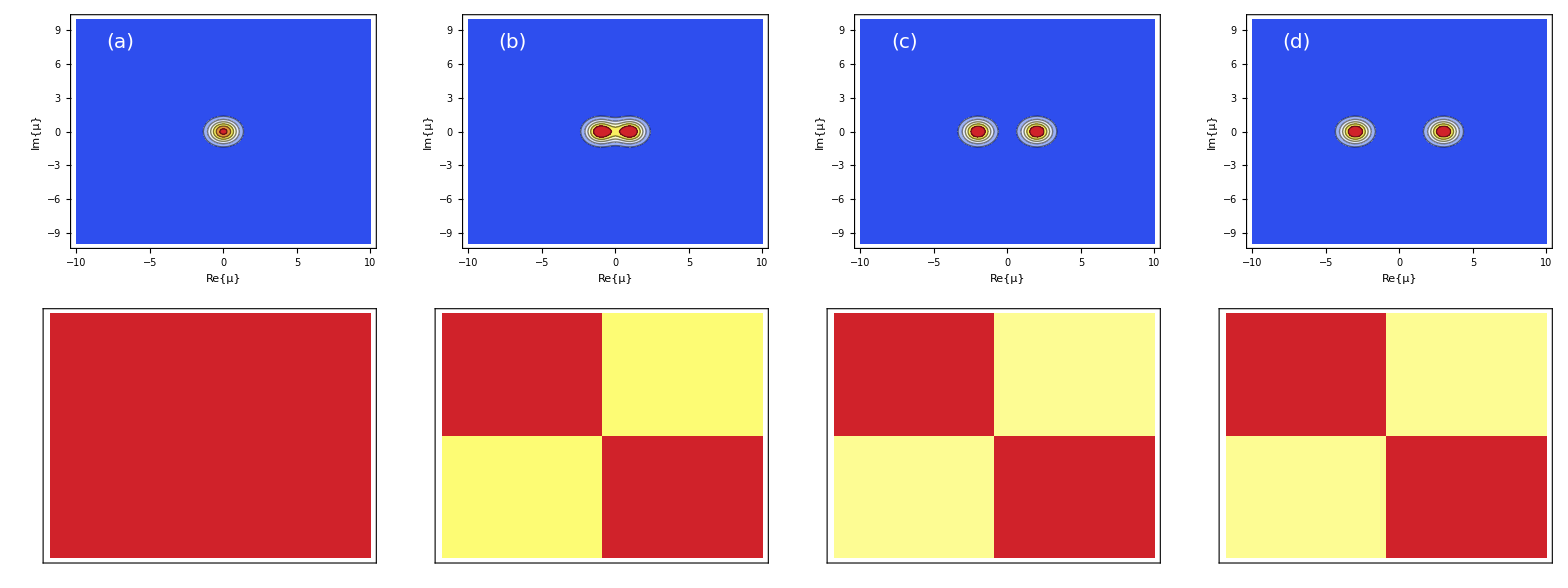

```mathematica
vNmodelExamplePlot1half=Grid[
{
(*Second row - Contour plot of the Q-function*)
Table[
Quiet@ContourPlot[Quiet@Q1half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},
Epilog->Inset[Style[alphabetlabel[[c+1]],White,FontSize->20],{-7,8}],
PlotPoints->40,
PlotRange->All,
ColorFunction->"TemperatureMap",
FrameLabel->{"Re{μ}","Im{μ}"},
AxesLabel->{"Re{α}","Im{α}"}],{c,{0,1,2,3}}]
,

(*First row - Hinton diagram of the density matrix*)
Table[MatrixPlot[ρt1half/.g0t->c,
FrameTicks->None,
ColorFunction->"TemperatureMap"],{c,{0,1,2,5}}]
}

]
Export[PlotsPathChap1<>"vNmodelExample1half.pdf",vNmodelExamplePlot1half];
```

```mathematica
Qplusonehalf=1/π(Exp[-Abs[(reμ + ⅈ imμ) - g0t/2 ]^2])//cf
Qminusonehalf=1/π(Exp[-Abs[(reμ + ⅈ imμ) + g0t/2 ]^2])//cf
```

(ⅇ^(-Abs[-g0t/2+ⅈ imμ+reμ]^2))/π

(ⅇ^(-Abs[g0t/2+ⅈ imμ+reμ]^2))/π

```mathematica
Integrate[Integrate[Qplusonehalf,{reμ,-20,20}],{imμ,-20,20}]
```

1/4 (Erf[20-Im[g0t]/2]+Erf[1/2 (40+Im[g0t])]) (Erf[20-Re[g0t]/2]+Erf[20+Re[g0t]/2])

```mathematica
1/4 (Erf[20-Im[g0t]/2]+Erf[1/2 (40+Im[g0t])]) (Erf[20-Re[g0t]/2]+Erf[20+Re[g0t]/2])//cf
```

1/2 Erf[20] (Erf[20-g0t/2]+Erf[20+g0t/2])

```mathematica
argOfintegral=√(Qplusonehalf Qminusonehalf)//cf
```

(ⅇ^(-g0t^2/4-imμ^2-reμ^2))/π

```mathematica
cBhatToyModel=Integrate[Integrate[argOfintegral,{reμ,-20,20}],{imμ,-20,20}]
```

ⅇ^(-g0t^2/4)

```mathematica
qℬhatToyModel=Abs[Tr[σx.ρt1half]]//cf
```

ⅇ^(-2 g0t^2)

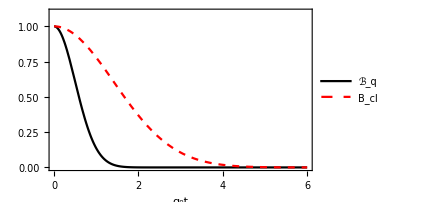

```mathematica
ToyModelcandqBhat=Plot[{qℬhatToyModel, cBhatToyModel},{g0t,0,6},
PlotStyle->{{Black},{Dashed,Red}},
PlotRange->{All,{0,1.1}},
PlotLegends->legend[{"ℬ_q","B_cl"},{0.85,0.8}],
FrameLabel->{"g_0t",None}]
```

```mathematica
Export[PlotsPathChap1<>"ToyModelcandqBhat.pdf",ToyModelcandqBhat];
```

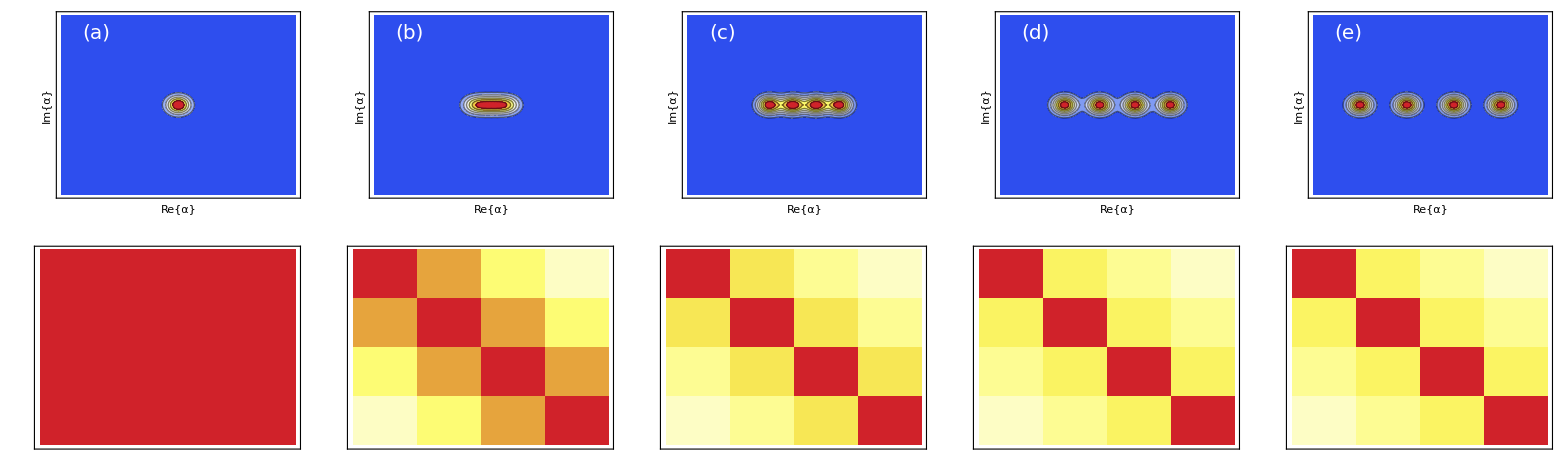

```mathematica
vNmodelExamplePlot3half=Grid[
{
(*First row - Contour plot of the Q-function*)
Table[
Quiet@ContourPlot[Quiet@Q3half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},
Epilog->Inset[Style[alphabetlabel[[c+1]],White,FontSize->20],{-7,8}],
PlotPoints->40,
PlotRange->All,
ColorFunction->"TemperatureMap",
FrameTicks->None,
AxesLabel->{"Re{α}","Im{α}"}],{c,{0,1,2,3,4}}],

(*Second row - Hinton diagram of the density matrix*)
Table[MatrixPlot[ρt3half/.g0t->c,
ColorFunction->"TemperatureMap",
PlotTheme->"Business",
FrameTicks->None,
FrameTicks->{{1,MX@" "},{2,MX@" "},{3,MX@" "},{4,MX@" "}}],{c,{0,1,2,3,4}}]

}

]
Export[PlotsPathChap1<>"vNmodelExample3half.pdf",vNmodelExamplePlot3half];
```

Playing with Manipulate:

```mathematica
Manipulate[
ContourPlot[Quiet@Q1half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->90,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset[Style["g_0t="<>ToString[c],White],{5,8}]],{c,0,5,0.01}]
```

```mathematica
Manipulate[
ContourPlot[Quiet@Q3half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->90,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset[Style["g_0t="<>ToString[c],White],{5,8}]],{c,0,5,0.01}]
```

Making cool gifs:

```mathematica
PrettyTiming[AnimQfunc=Table[Quiet@ContourPlot[Quiet@Q1half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->40,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset[Style["g_0t="<>ToString[c],FontSize->30],{5,8}]],{c,0,5,0.1}];
Animρt=Table[
MatrixPlot[ρt1half/.g0t->c,ColorFunction->"TemperatureMap",Epilog->Inset["g_0t="<>ToString[c],{5,8}]],
{c,0,5,0.1}];]
```

0h : 0m : 9s

```mathematica
Export[PlotsPathChap1<>"GifQfunction1half.gif",AnimQfunc];
Export[PlotsPathChap1<>"GifDensityMatrix1half.gif",Animρt];
```

```mathematica
PrettyTiming[AnimQfunc=Table[Quiet@ContourPlot[Quiet@Q3half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->40,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset["g_0t="<>ToString[c],{5,8}]],{c,0,5,0.1}];
Animρt=Table[
MatrixPlot[ρt3half/.g0t->c,ColorFunction->"TemperatureMap",Epilog->Inset["g_0t="<>ToString[c],{5,8}]],
{c,0,5,0.1}];]
```

0h : 0m : 18s

```mathematica
Export[PlotsPathChap1<>"GifQfunction3half.gif",AnimQfunc];
Export[PlotsPathChap1<>"GifDensityMatrix3half.gif",Animρt];
```